```mathematica
Get["linearModel`"]
```

its alive

its alive

its alive

«4 more identical outputs»

datum::shdw: Symbol datum appears in multiple contexts {linearModel`,Global`}; definitions in context linearModel` may shadow or be shadowed by other definitions.

plot::shdw: Symbol plot appears in multiple contexts {linearModel`,Global`}; definitions in context linearModel` may shadow or be shadowed by other definitions.

error::shdw: Symbol error appears in multiple contexts {linearModel`,Global`}; definitions in context linearModel` may shadow or be shadowed by other definitions.

annotatedTune::shdw: Symbol annotatedTune appears in multiple contexts {linearModel`,Global`}; definitions in context linearModel` may shadow or be shadowed by other definitions.

```mathematica
annotatedTune[f_]:=(r=Range[-5,15,.1];Show[plot[datum~Join~Thread[{r,First[f@#]&/@r}]],Epilog->Text[error[f],{10,0.9},{-1,0}]])
```

```mathematica
net=NetInitialize[NetChain[{
(*Implicit LinearLayer[1]*) 
LinearLayer[1000],
Tanh,
LinearLayer[1000],
Ramp,


LinearLayer[1]
},"Input"->1]]
```

NetChain[<>]

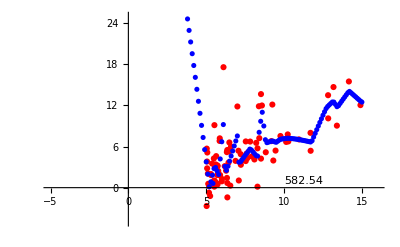

```mathematica
model=NetTrain[net,format/@datum,
Method->{"ADAM","LearningRate"->0.001},BatchSize->Length[datum],TargetDevice->{"GPU",3},
MaxTrainingRounds->Quantity[30,"Seconds"],TrainingProgressReporting->{Function[annotatedTune[#Net]],"Interval"->Quantity[1,"Seconds"]}];
annotatedTune[model]
```